```mathematica
(* 01 *)
ParallelEvaluate[RandomInteger[{0,25}]]
```

{21,17,19,18,20,21,13,3}

```mathematica
(* 02 *)
var25 = Table[RandomInteger[{1,25}],5]
ParallelEvaluate[var25^2]
```

{22,11,11,15,11}

{{484,121,121,225,121},{484,121,121,225,121},{484,121,121,225,121},{484,121,121,225,121},{484,121,121,225,121},{484,121,121,225,121},{484,121,121,225,121},{484,121,121,225,121}}

```mathematica
(* 03 *)
```

```mathematica
ParallelEvaluate[var25=RandomInteger[{1,25},5];var25^2]
```

{{289,121,256,100,1},{324,576,36,196,100},{529,625,100,196,400},{4,625,144,144,289},{529,576,64,64,225},{36,64,4,100,81},{49,64,324,484,256},{49,16,225,324,144}}

```mathematica
(* 04 *)
Table[ParallelSubmit[(i),FindRoot[Sin[x]+ⅇ^x==0,{x,i}]],{i,-3,3,1}]
```

{ParallelSubmit[i,FindRoot[Sin[x]+ⅇ^x==0,{x,i}]],ParallelSubmit[i,FindRoot[Sin[x]+ⅇ^x==0,{x,i}]],ParallelSubmit[i,FindRoot[Sin[x]+ⅇ^x==0,{x,i}]],ParallelSubmit[i,FindRoot[Sin[x]+ⅇ^x==0,{x,i}]],ParallelSubmit[i,FindRoot[Sin[x]+ⅇ^x==0,{x,i}]],ParallelSubmit[i,FindRoot[Sin[x]+ⅇ^x==0,{x,i}]],ParallelSubmit[i,FindRoot[Sin[x]+ⅇ^x==0,{x,i}]]}

```mathematica
(* 05 *)
Table[ParallelSubmit[{i},FindRoot[Sin[x]+ⅇ^x==0,{x,i}]],{i,-3,3,1}]
```

{FindRoot[Sin[x]+«1»==0,«1»]
,FindRoot[Sin[x]+«1»==0,«1»]
,FindRoot[Sin[x]+«1»==0,«1»]
,FindRoot[Sin[x]+«1»==0,«1»]
,FindRoot[Sin[x]+«1»==0,«1»]
,FindRoot[Sin[x]+«1»==0,«1»]
,FindRoot[Sin[x]+«1»==0,«1»]
}

```mathematica
WaitAll[%]
```

{{x→-3.09636},{x→-3.09636},{x→-0.588533},{x→-0.588533},{x→-0.588533},{x→-0.588533},{x→-0.588533}}

```mathematica
(* 06 *)
ParallelTable[FindRoot[Sin[x]+ⅇ^x,{x,i}],{i,-3,3,1}]
```

{{x→-3.09636},{x→-3.09636},{x→-0.588533},{x→-0.588533},{x→-0.588533},{x→-0.588533},{x→-0.588533}}

```mathematica
(* 07 *)
ParallelTable[Plot3D[Sin[x]Cos[a *y],{x,-π,π},{y,-π,π}],{a,1,3,1}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

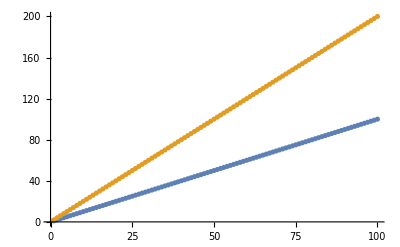
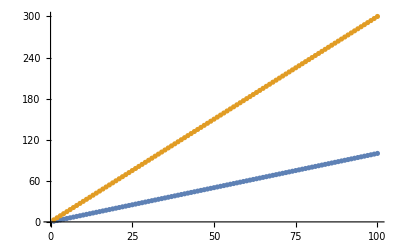
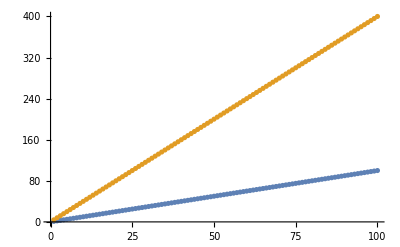
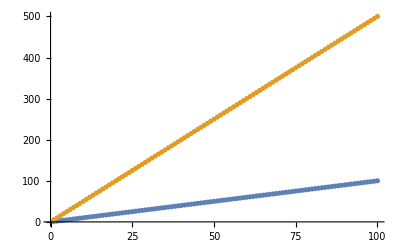

```mathematica
(* 08 *)
ParallelTable[ListPlot[{Range[100],i*Range[100]}],{i,2,5,1}]
```